```mathematica
f = 0.610774x^2Sin[x] - Sin[x] + x Cos[x]
```

x Cos[x]-Sin[x]+0.610774 x^2 Sin[x]

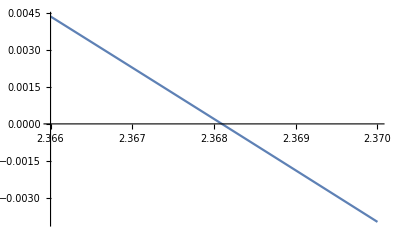

```mathematica
Plot[f, {x, 2.366, 2.37}]
```

```mathematica
T = DSolve[A(y[x] + x y'[x])-x^(3/2)y[x]^(9/2) == 0,y[x],x]
```

{{y[x]→2^(4/7)/(((x^(3/2) (7+4 A x^2 C[1]))/A)^(2/7))}}

```mathematica
Plot[T[x], {x, 0, 10}]
```

-Graphics-

NDSolve::deqn: Equation or list of equations expected instead of False in the first argument {Sin[y[x]] y[x]+y''[x]==0,False,y'[0]==0}.

```mathematica
s=NDSolve[{y'[x]==y[x]Cos[x+y[x]],y[0]==1},y,{x,0,30}]
```

NDSolve::ndnco: The number of constraints (0) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (1).

NDSolve::deqn: Equation or list of equations expected instead of False in the first argument {Sin[y[x]] y[x]+y''[x]==0,False,y'[0]==0}.